```mathematica
AllGraphs[k_]:=Block[{edges=Subsets[Range[k],{2}],combinations, total, current,result},

combinations=Subsets[edges];
total=Length[combinations];
current=0;
Monitor[
result=Select[
Table[
current++;
Graph[Range[k],e, VertexLabels->"Name"],
{e,combinations}
],
ConnectedGraphQ[#]&
],
{current,total}
];
PrintTemporary["Graphs found ", k, " --", Length[result]];
result
]
```

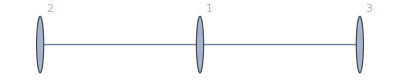
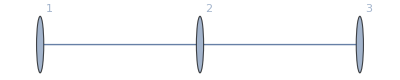
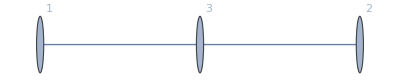
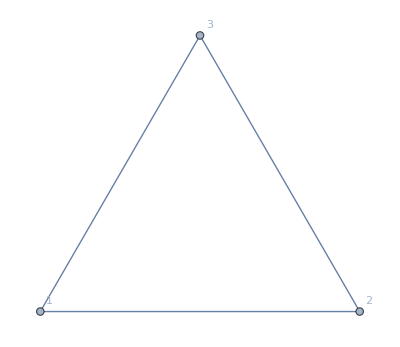

```mathematica
AllGraphs[3]
```

```mathematica
FormulaGraph2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[Framed[SymbolToLabel2[ SetsToSymbol[s],10],Background->White],-Pi/4],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{300,200},AspectRatio->Automatic]
]
```

```mathematica
CountFor[set_,c_]:=Length[Select[set,StringCount[SymbolName[#],"x"]+1==c&]]
```

```mathematica
Table[
Table[
Framed[
Labeled[
CompleteGraph[VertexCount[gen[[1]]],GraphHighlight->EdgeList[GraphComplement[gen[[1]]]],GraphHighlightStyle->{Red,"Thick"}, VertexLabels->"Name"]
->
Graph[FormulaGraph2[gen[[2]]],ImageSize->Medium,AspectRatio->Automatic],
{gen[[2]],CompleteBaseCoeff[ ChromaticPolynomial[gen[[1]],x]]},
{Bottom,Top}]],
{gen,Table[{g,FindFullFormula[g]},{g,Map[First,Tally[Select[AllGraphs[count],ConnectedGraphQ[#]&&ChromaticPolynomial[#,3]==6&&ChromaticPolynomial[#,2]==0&],IsomorphicGraphQ]]}]}
],
{count,3,7}
]
```

$Aborted[]

```mathematica
SymbolToSets[v15x234]
```

{{1,5},{2,3,4}}

```mathematica
SymbolToSets[v1x23x45]
```

{{1},{2,3},{4,5}}

```mathematica
IsRefinement[SymbolToSets[v15x234],SymbolToSets[v1x23x45]]
```

False

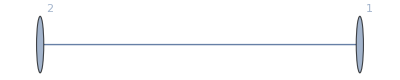
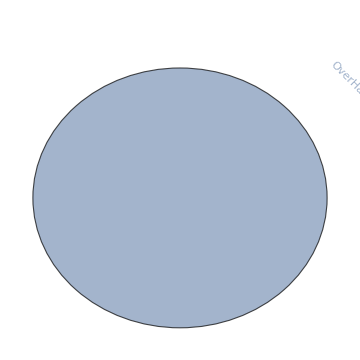
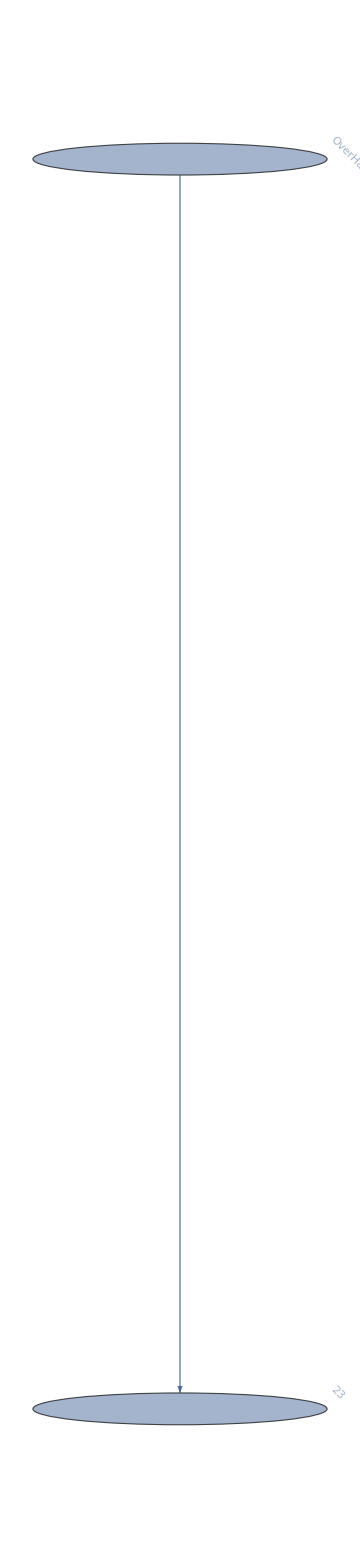
{{-Graphics-→-Graphics-{v1x2}{0,0,1}},{-Graphics-→-Graphics-{v1x2x3,v1x23}{0,0,1,1}}}

```mathematica
Table[
Table[
Framed[
Labeled[
CompleteGraph[VertexCount[gen[[1]]],GraphHighlight->EdgeList[GraphComplement[gen[[1]]]],GraphHighlightStyle->{Red,"Thick"}, VertexLabels->"Name"]
->
Graph[FormulaGraph2[gen[[2]]],ImageSize->Medium,AspectRatio->Automatic],
{gen[[2]],CompleteBaseCoeff[ ChromaticPolynomial[gen[[1]],x]]},
{Bottom,Top}]],
{gen,Table[{g,FindFullFormula[g]},{g,Map[First,Tally[Select[AllGraphs[count],ConnectedGraphQ[#]&&ChromaticPolynomial[#,2]==2&&ChromaticPolynomial[#,1]==0&],IsomorphicGraphQ]]}]}
],
{count,2,3}
]
```

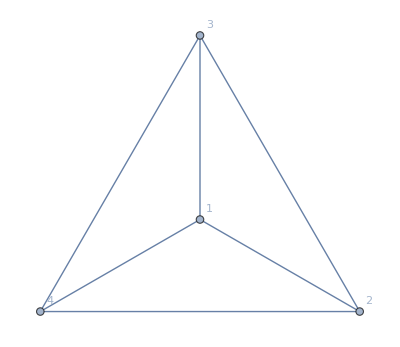
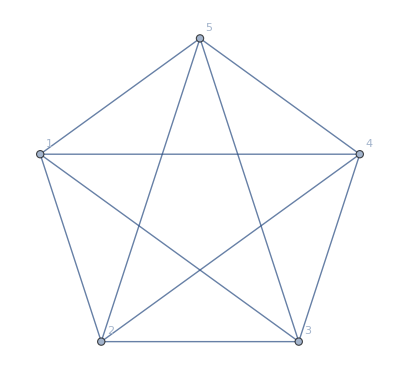
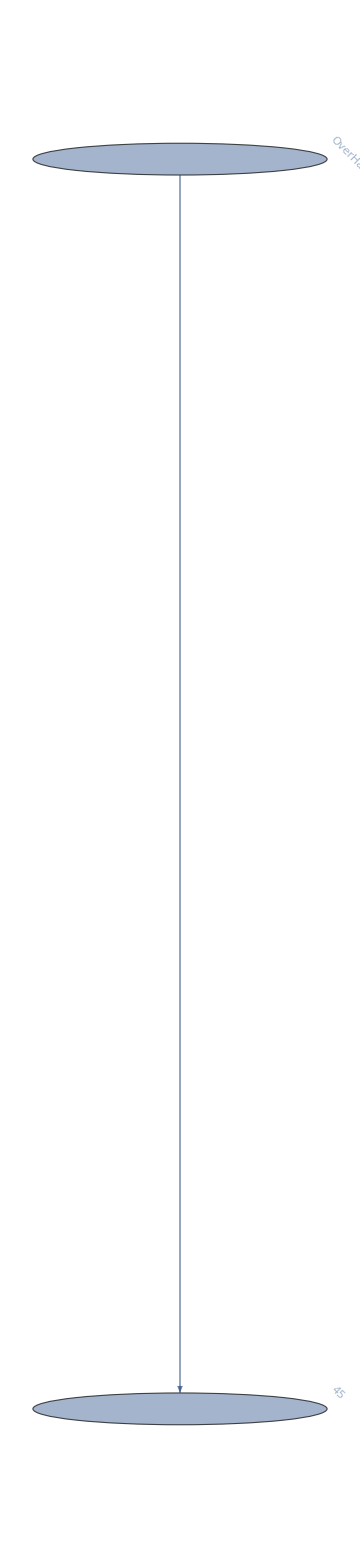
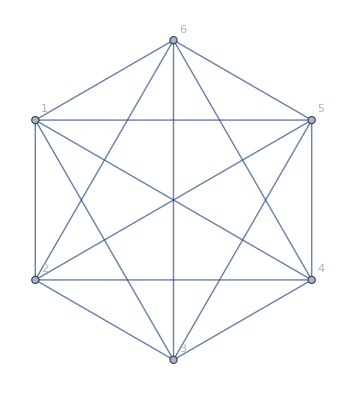
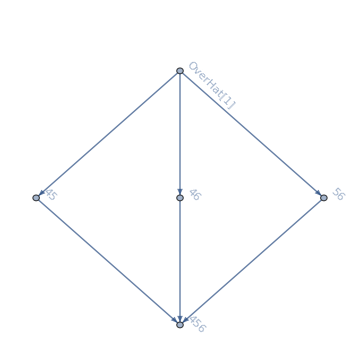
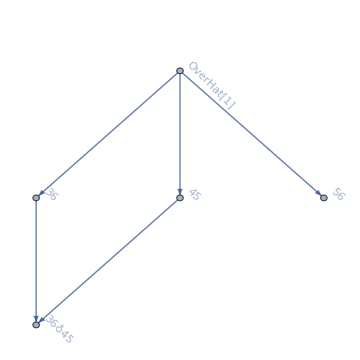
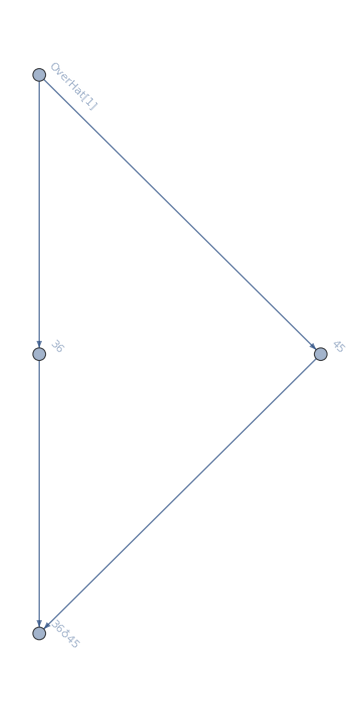
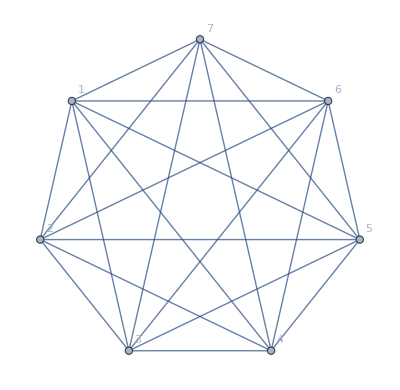
{{-Graphics-→-Graphics-{v1x2x3x4}{0,0,0,0,1}},{-Graphics-→-Graphics-{v1x2x3x4x5,v1x2x3x45}{0,0,0,0,1,1}},{-Graphics-→-Graphics-{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x3x456}{0,0,0,0,1,3,1},-Graphics-→-Graphics-{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x45x6,v1x2x36x4x5,v1x2x36x45}{0,0,0,0,1,3,1},-Graphics-→-Graphics-{v1x2x3x4x5x6,v1x2x3x45x6,v1x2x36x4x5,v1x2x36x45}{0,0,0,0,1,2,1}},{-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x57x6,v1x2x3x4x56x7,v1x2x3x4x567,v1x2x3x47x5x6,v1x2x3x47x56,v1x2x3x46x5x7,v1x2x3x467x5,v1x2x3x46x57,v1x2x3x45x6x7,v1x2x3x457x6,v1x2x3x456x7,v1x2x3x45x67,v1x2x3x4567}{0,0,0,0,1,7,6,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x57x6,v1x2x3x4x56x7,v1x2x3x4x567,v1x2x3x46x5x7,v1x2x3x46x57,v1x2x3x45x6x7,v1x2x3x456x7,v1x2x3x45x67,v1x2x37x4x5x6,v1x2x37x4x56,v1x2x37x46x5,v1x2x37x45x6,v1x2x37x456}{0,0,0,0,1,7,6,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x56x7,v1x2x3x47x5x6,v1x2x3x47x56,v1x2x3x45x6x7,v1x2x3x45x67,v1x2x37x4x5x6,v1x2x37x4x56,v1x2x37x45x6,v1x2x36x4x5x7,v1x2x367x4x5,v1x2x36x47x5,v1x2x36x45x7,v1x2x367x45}{0,0,0,0,1,7,6,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x57x6,v1x2x3x4x56x7,v1x2x3x4x567,v1x2x3x45x6x7,v1x2x3x45x67,v1x2x36x4x5x7,v1x2x36x4x57,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x4x56,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,7,6,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x56x7,v1x2x3x47x5x6,v1x2x3x47x56,v1x2x3x45x6x7,v1x2x3x45x67,v1x2x36x4x5x7,v1x2x36x47x5,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x4x56,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,7,6,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x56x7,v1x2x3x47x5x6,v1x2x3x47x56,v1x2x3x45x6x7,v1x2x37x4x5x6,v1x2x37x4x56,v1x2x37x45x6,v1x2x36x4x5x7,v1x2x36x47x5,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x4x56,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,8,6,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x56x7,v1x2x3x46x5x7,v1x2x3x45x6x7,v1x2x3x456x7,v1x2x3x45x67,v1x2x37x4x5x6,v1x2x37x4x56,v1x2x37x46x5,v1x2x37x45x6,v1x2x37x456}{0,0,0,0,1,5,5,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x57x6,v1x2x3x45x6x7,v1x2x3x45x67,v1x2x36x4x5x7,v1x2x36x4x57,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,5,5,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x56x7,v1x2x3x47x5x6,v1x2x3x47x56,v1x2x3x45x6x7,v1x2x36x4x5x7,v1x2x36x47x5,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x4x56,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,6,5,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x56x7,v1x2x3x46x5x7,v1x2x3x45x6x7,v1x2x3x456x7,v1x2x37x4x5x6,v1x2x37x4x56,v1x2x37x46x5,v1x2x37x45x6,v1x2x37x456}{0,0,0,0,1,4,4,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x45x6x7,v1x2x3x45x67,v1x2x36x4x5x7,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,4,4,1},-Graphics-→-Graphics-{v1x2x3x4x5x6x7,v1x2x3x45x6x7,v1x2x36x4x5x7,v1x2x36x45x7,v1x27x3x4x5x6,v1x27x3x45x6,v1x27x36x4x5,v1x27x36x45}{0,0,0,0,1,3,3,1}}}

```mathematica
Table[
Table[
Framed[
Labeled[
CompleteGraph[VertexCount[gen[[1]]],GraphHighlight->EdgeList[GraphComplement[gen[[1]]]],GraphHighlightStyle->{Red,"Thick"}, VertexLabels->"Name"]
->
Graph[FormulaGraph2[gen[[2]]],ImageSize->Medium,AspectRatio->Automatic],
{gen[[2]],CompleteBaseCoeff[ ChromaticPolynomial[gen[[1]],x]]},
{Bottom,Top}]],
{gen,Table[{g,FindFullFormula[g]},{g,Map[First,Tally[Select[AllGraphs[count],ConnectedGraphQ[#]&&ChromaticPolynomial[#,4]==24&&ChromaticPolynomial[#,3]==0&],IsomorphicGraphQ]]}]}
],
{count,4,7}
]
```